```mathematica
SolveWK[θ_,F̂ :_]:=Block[{U2Sol,U1Sol,Subscript[U, 1],Subscript[U, 2]},
U2Sol=NDSolve[{-2  Subscript[U, 2]'[X] Subscript[U, 2]'[X] Subscript[U, 2]''[X]+2  (-(F̂ α Sin[θ])-(Subscript[U, 2]'[X])^2/2) Subscript[U, 2]''[X]+3  (Subscript[U, 2]'[X])^2 Subscript[U, 2]''[X]-2 α Derivative[4][Subscript[U, 2]][X]==0,Subscript[U, 2][0]==0,Subscript[U, 2]'[0]==0,- Subscript[U, 2]''[1]==0,- Subscript[U, 2]'''[1]==-F̂ Cos[θ]},Subscript[U, 2],{X,0,1}][[1]];
U1Sol=NDSolve[{-F̂ α Sin[θ]==Subscript[U, 1]'[X]+(Subscript[U, 2]'[X]/.U2Sol)^2/2,Subscript[U, 1][0]==0},Subscript[U, 1],{X,0,1}][[1]];
{-Subscript[U, 1][1]/.U1Sol,-Subscript[U, 2][1]/.U2Sol}
]
```

```mathematica
<<Notation`
Symbolize[Subscript[x_, y_]];
Symbolize[OverHat[x_]];
```

```mathematica
<<VariationalMethods`
```

```mathematica
ClearAll[Ε ,Ι,A,F]
```

```mathematica
EulerEquations[(Ε Ι)/2 (Subscript[U, 2]''[X])^2+ Ε A/2(Subscript[U, 1]'[X]+1/2 (Subscript[U, 2]'[X])^2)^2+P  Subscript[U, 2]'[X],{Subscript[U, 1][X],Subscript[U, 2][X]},X]
```

{-A Ε (U_1''[X]+U_2'[X] U_2''[X])==0,-1/2 Ε (2 A U_2'[X] U_1''[X]+2 A U_1'[X] U_2''[X]+3 A U_2'[X]^2 U_2''[X]-2 Ι U_2^(4)[X])==0}

```mathematica
2(-1/2 Ε (2 A Subscript[U, 2]'[X] Subscript[U, 1]''[X]+2 A Subscript[U, 1]'[X] Subscript[U, 2]''[X]+3 A (Subscript[U, 2]'[X])^2 Subscript[U, 2]''[X]-2 Ι Derivative[4][Subscript[U, 2]][X]))
```

-Ε (2 A U_2'[X] U_1''[X]+2 A U_1'[X] U_2''[X]+3 A U_2'[X]^2 U_2''[X]-2 Ι U_2^(4)[X])

### NDSolve not working

```mathematica
Block[{Ε=1,A=1,Ι=0.0025},NDSolve[{ (Subscript[U, 1]''[X]+Subscript[U, 2]'[X] Subscript[U, 2]''[X])==0,2 A Subscript[U, 2]'[X] Subscript[U, 1]''[X]+2 A Subscript[U, 1]'[X] Subscript[U, 2]''[X]+3 A (Subscript[U, 2]'[X])^2 Subscript[U, 2]''[X]-2 Ι Derivative[4][Subscript[U, 2]][X]==0,Subscript[U, 1][0]==0,Subscript[U, 2][0]==0,Subscript[U, 2]'[0]==0,Subscript[U, 1][1]==0, Subscript[U, 2][1]==0.01, Subscript[U, 2]'[1]==0},{Subscript[U, 1][X],Subscript[U, 2][X]},{X,0,1}]
]
```

$Aborted

```mathematica
ClearAll[α]
```

```mathematica
SolU2 =DSolve[{T Subscript[U, 2][X]-α Subscript[U, 2]''[X]==C1 X+C2,Subscript[U, 2][0]==0,Subscript[U, 2]'[0]==0},Subscript[U, 2],X][[1]]
```

{U_2→Function[{X},-(ⅇ^(-(√T X)/(√α)) (C2 √T-2 C2 ⅇ^((√T X)/(√α)) √T+C2 ⅇ^((2 √T X)/(√α)) √T-2 C1 ⅇ^((√T X)/(√α)) √T X-C1 √α+C1 ⅇ^((2 √T X)/(√α)) √α))/(2 T^(3/2))]}

```mathematica
Evaluate[Subscript[U, 2]'[1]/.SolU2]//Simplify
```

-(ⅇ^(-(√T)/(√α)) (-1+ⅇ^((√T)/(√α))) (C2 (1+ⅇ^((√T)/(√α))) √T+C1 (-1+ⅇ^((√T)/(√α))) √α))/(2 T √α)

```mathematica
SolC1=Solve[Evaluate[Subscript[U, 2]'[1]/.SolU2]==0,C1][[1]]
```

{C1→-(C2 (1+ⅇ^((√T)/(√α))) √T)/((-1+ⅇ^((√T)/(√α))) √α)}

```mathematica
Integrate[T-1/2 FullSimplify[Subscript[U, 2]'[X]/.SolU2/.SolC1]^2,{X,0,1}]
```

T-(C2^2 Csch[(√T)/(2 √α)]^2 (2+Cosh[(√T)/(√α)]-(3 √α Sinh[(√T)/(√α)])/(√T)))/(4 T α)

```mathematica
SolC2=Solve[T-(C2^2 Csch[(√T)/(2 √α)]^2 (2+Cosh[(√T)/(√α)]-(3 √α Sinh[(√T)/(√α)])/(√T)))/(4 T α)==0,C2]
```

{{C2→-(2 √T)/(√((2 Csch[(√T)/(2 √α)]^2)/(T α)+(Cosh[(√T)/(√α)] Csch[(√T)/(2 √α)]^2)/(T α)-(3 Csch[(√T)/(2 √α)]^2 Sinh[(√T)/(√α)])/(T^(3/2) √α)))},{C2→(2 √T)/(√((2 Csch[(√T)/(2 √α)]^2)/(T α)+(Cosh[(√T)/(√α)] Csch[(√T)/(2 √α)]^2)/(T α)-(3 Csch[(√T)/(2 √α)]^2 Sinh[(√T)/(√α)])/(T^(3/2) √α)))}}

```mathematica
Simplify[Evaluate[Subscript[U, 2][1]/.SolU2]/.SolC1/.SolC2[[1]]]
```

(2 (1+ⅇ^((√T)/(√α))) √T-4 (-1+ⅇ^((√T)/(√α))) √α)/((-1+ⅇ^((√T)/(√α))) √T √α √((Csch[(√T)/(2 √α)]^2 (2 √T+√T Cosh[(√T)/(√α)]-3 √α Sinh[(√T)/(√α)]))/(T^(3/2) α)))

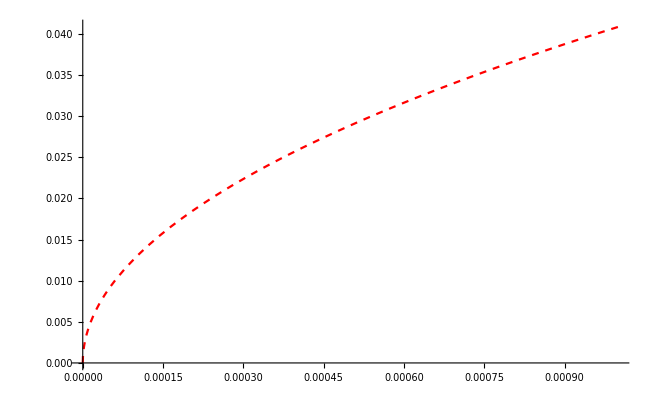

```mathematica
Block[{α=0.0025},
Plot[Simplify[Evaluate[Subscript[U, 2][1]/.SolU2]/.SolC1/.SolC2[[1]]],{T,0,0.001},PlotStyle->{Dashed,Red}]
(*Simplify[Evaluate[Subscript[U, 2][1]/.SolU2]/.SolC1/.SolC2[[1]]]//N*)
]
```

```mathematica
Tlist = Array[(#/1000.)^2&,200];
```

```mathematica
Tlist//Length
```

200

```mathematica
δList = Table[Block[{α=0.0025},
Simplify[Evaluate[Subscript[U, 2][1]/.SolU2]/.SolC1/.SolC2[[1]]]
(*Simplify[Evaluate[Subscript[U, 2][1]/.SolU2]/.SolC1/.SolC2[[1]]]//N*)
],{T,Tlist}];
w0 = δList/2;
```

```mathematica
Plist =Table[Block[{α=0.0025},
Simplify[Evaluate[Subscript[U, 2]'''[1]/.SolU2]/.SolC1/.SolC2[[1]]]
],{T,Tlist}];
F=-8Plist;
```

```mathematica
WKSol = Transpose[{w0,F}];
```

```mathematica
SetDirectory[NotebookDirectory[]]
DumpSave["data/WKSol.mx",WKSol];
```

/Users/wenqiangfang/Dropbox (Brown)/Apps/Sawtooth_Pattern_PartII Theory/ResearchNote

```mathematica
ClearAll[WKSol];
<<"data/WKSol.mx"
```

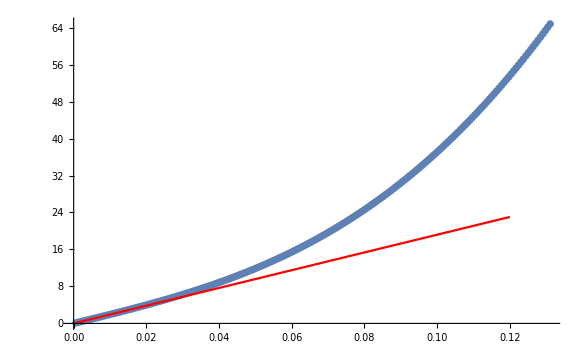

```mathematica
Show[ListPlot[WKSol],
Plot[192x,{x,0,0.12},PlotStyle->Red]]
```